## numerical derivatives

```mathematica
getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[3,1]]]/2;
frames=Length[t[[3]]];
times=Flatten[t[[1]]];
types=t[[4,1]];
positions={};
Do[
posSet=t[[3,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];
```

```mathematica
temp=getData["/Users/dmsussma/repos/test.nc"];
```

```mathematica
p=temp[[3,Length[temp[[3]]]]];
vm=VoronoiMesh[p];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

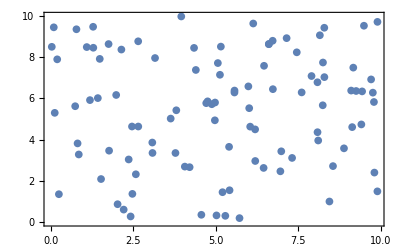

```mathematica
ListPlot[p]
```

```mathematica
dx=0.0001;
p2=p;
p2[[27]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
Vneighs=Length@@@cells;
(Vareas[[20]]-VareasI[[20]])/dx
(Vperis[[20]]-VperisI[[20]])/dx
```

-0.442964

-4.06435

```mathematica
vm=VoronoiMesh[p];
dl=ListPlot[Table[{p[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
dl=ListPlot[Table[{p[[i]]},{i,1,79}],PlotMarkers->Table[i,{i,1,79}]];
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl]
```

```mathematica
Vareas=PropertyValue[{vm,2},MeshCellMeasure];
Vperis=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
Vneighs=Length@@@cells;
```

```mathematica
Vareas[[20]]
Vperis[[20]]
```

1.11296

4.5647

```mathematica
ai
```

1.1134

-0.0024662

-0.00225958

```mathematica
area22xx[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v11=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v10=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v01=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v00=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
area22yy[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v11=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v10=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v01=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v00=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
area22xy[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v11=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v10=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v01=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v00=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
area22yx[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v11=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v10=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v01=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v00=Sum[(Vareas[[cellset[[i]]]]-1)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
peri22xx[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v11=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v10=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v01=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v00=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
peri22yy[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v11=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v10=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v01=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v00=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
peri22xy[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v11=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v10=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v01=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v00=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
peri22yx[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v11=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,dx};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v10=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v01=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={0,-dx};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vperis=RegionMeasure/@(MeshPrimitives[vm2,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
v00=Sum[(Vperis[[cellset[[i]]]]-4)^2,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
```

```mathematica
cells={20};
a=27;
b=26;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
cells={20,100,93,27,78,76};
a=27;
b=26;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
```

(0.244897 | 0.246931
-0.0914989 | -0.0865226)

(0.68923 | -0.0823649
-0.542362 | 0.0283515)

```mathematica
cells={20,100,93,27,78,76};
a=27;
b=54;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
```

(-0.304246 | 0.286992
0.28543 | -0.19321)

```mathematica
cells={20};
a=27;
b=26;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
cells={20,100,93,27,78,76};
a=27;
b=26;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
cells={20,100,93,27,78,76};
cells=Table[i,{i,1,100}];
a=27;
b=26;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
```

(0.244897 | 0.246931
-0.0914989 | -0.0865226)

(0.68923 | -0.0823649
-0.542362 | 0.0283515)

(0.688942 | -0.0818545
-0.541718 | 0.0272848)

```mathematica
ddx=10^-4;
cells={20};
cells={20,100,93,27,78,76};
a=27;
b=27;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
```

```mathematica
ddx=10^-6;
cells={20};
cells={20,100,93,27,78,76};
a=27;
b=27;
({{peri22xx[cells,a,b,ddx], peri22xy[cells,a,b,ddx]}, {peri22yx[cells,a,b,ddx], peri22yy[cells,a,b,ddx]}})//MatrixForm
cells={20};
cells={20,100,93,27,78,76};
a=27;
b=26;
({{peri22xx[cells,a,b,ddx], peri22xy[cells,a,b,ddx]}, {peri22yx[cells,a,b,ddx], peri22yy[cells,a,b,ddx]}})//MatrixForm
cells={20};
cells={20,100,93,27,78,76};
a=27;
b=54;
({{peri22xx[cells,a,b,ddx], peri22xy[cells,a,b,ddx]}, {peri22yx[cells,a,b,ddx], peri22yy[cells,a,b,ddx]}})//MatrixForm
```

(76.9933 | -64.6894
-64.6894 | 46.8627)

(3.26117 | 1.59361
-0.0284217 | -0.933476)

(-0.460854 | 0.285216
0.670908 | -0.271894)

```mathematica
ddx=10^-4;

(* example of 2nd nearest neighbor*)
cells={20,100,93,27,78,76};
a=27;
b=54;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
```

(-0.304246 | 0.286992
0.285428 | -0.193206)

```mathematica
cell=20;
a=27;
b=27;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

voronoi position derivatives

```mathematica
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
]
```

```mathematica
hijk=voro[{rix,riy},{rjx,rjy},{rkx,rky}];
```

```mathematica
v1d[r1_,r2_,r3_]:=(({{D[hijk[[1]],rix], D[hijk[[1]],riy]}, {D[hijk[[2]],rix], D[hijk[[2]],riy]}}))/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]}
v2d[r1_,r2_,r3_]:={D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx],
D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx],
D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy],
D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]}
```

```mathematica
v1d[p[[26]],p[[27]],p[[50]]]//MatrixForm
v2d[p[[27]],p[[26]],p[[21]]]//MatrixForm
```

(-0.0853456 | -0.256611
0.217085 | 0.652714)

(-0.710562
-0.773193
0.532421
-0.0154744
-0.459514
-0.349779
0.778153
0.0403389)

```mathematica
(* first derivatives *)
c=26;
b=27;
g=50;
DDx={0.0001,0};
DDy={0,0.0001};
cartesian=1;
xx=(voro[p[[c]]+DDx,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.0001);
xy=(voro[p[[c]]+DDy,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.0001);
cartesian=2;
yx=(voro[p[[c]]+DDx,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.0001);
yy=(voro[p[[c]]+DDy,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.0001);
({{xx, xy}, {yx, yy}})//MatrixForm
```

(-0.0853213 | -0.256617
0.217023 | 0.65273)

```mathematica
DDx={0.0001,0};
DDy={0,0.0001};

c=27;
b=26;
g=50;
(voro[p[[c]]+DDx,p[[b]]+DDx,p[[g]]][[1]]+voro[p[[c]]-DDx,p[[b]]-DDx,p[[g]]][[1]]-voro[p[[c]]-DDx,p[[b]]+DDx,p[[g]]][[1]]-
voro[p[[c]]+DDx,p[[b]]-DDx,p[[g]]][[1]])/(4*0.0001^2)

(voro[p[[c]]+DDx,p[[b]]+DDx,p[[g]]][[2]]+voro[p[[c]]-DDx,p[[b]]-DDx,p[[g]]][[2]]-voro[p[[c]]-DDx,p[[b]]+DDx,p[[g]]][[2]]-
voro[p[[c]]+DDx,p[[b]]-DDx,p[[g]]][[2]])/(4*0.0001^2)

(voro[p[[c]]+DDy,p[[b]]+DDx,p[[g]]][[1]]+voro[p[[c]]-DDy,p[[b]]-DDx,p[[g]]][[1]]-voro[p[[c]]-DDy,p[[b]]+DDx,p[[g]]][[1]]-
voro[p[[c]]+DDy,p[[b]]-DDx,p[[g]]][[1]])/(4*0.0001^2)

(voro[p[[c]]+DDy,p[[b]]+DDx,p[[g]]][[2]]+voro[p[[c]]-DDy,p[[b]]-DDx,p[[g]]][[2]]-voro[p[[c]]-DDy,p[[b]]+DDx,p[[g]]][[2]]-
voro[p[[c]]+DDy,p[[b]]-DDx,p[[g]]][[2]])/(4*0.0001^2)

(voro[p[[c]]+DDx,p[[b]]+DDy,p[[g]]][[1]]+voro[p[[c]]-DDx,p[[b]]-DDy,p[[g]]][[1]]-voro[p[[c]]-DDx,p[[b]]+DDy,p[[g]]][[1]]-
voro[p[[c]]+DDx,p[[b]]-DDy,p[[g]]][[1]])/(4*0.0001^2)

(voro[p[[c]]+DDx,p[[b]]+DDy,p[[g]]][[2]]+voro[p[[c]]-DDx,p[[b]]-DDy,p[[g]]][[2]]-voro[p[[c]]-DDx,p[[b]]+DDy,p[[g]]][[2]]-
voro[p[[c]]+DDx,p[[b]]-DDy,p[[g]]][[2]])/(4*0.0001^2)

(voro[p[[c]]+DDy,p[[b]]+DDy,p[[g]]][[1]]+voro[p[[c]]-DDy,p[[b]]-DDy,p[[g]]][[1]]-voro[p[[c]]-DDy,p[[b]]+DDy,p[[g]]][[1]]-
voro[p[[c]]+DDy,p[[b]]-DDy,p[[g]]][[1]])/(4*0.0001^2)

(voro[p[[c]]+DDy,p[[b]]+DDy,p[[g]]][[2]]+voro[p[[c]]-DDy,p[[b]]-DDy,p[[g]]][[2]]-voro[p[[c]]-DDy,p[[b]]+DDy,p[[g]]][[2]]-
voro[p[[c]]+DDy,p[[b]]-DDy,p[[g]]][[2]])/(4*0.0001^2)
```

-0.0510012

0.3509

-0.372988

0.386154

0.14837

0.287615

-0.651703

-0.033845

```mathematica
(* first derivatives *)
c=21;
b=27;
g=79;
cartesian=1;
xx=(voro[p[[c]]+DDx,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.00001);
xy=(voro[p[[c]]+DDy,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.00001);
cartesian=2;
yx=(voro[p[[c]]+DDx,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.00001);
yy=(voro[p[[c]]+DDy,p[[b]],p[[g]]][[cartesian]]-voro[p[[c]],p[[b]],p[[g]]][[cartesian]])/(0.00001);
({{xx, xy}, {yx, yy}})//MatrixForm
```

## analytic derivatives

```mathematica
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
hijk=voro[ri,rj,rk]
```

```mathematica
ri
rj
rk
```

{rix,riy}

{rjx,rjy}

{rkx,rky}

```mathematica
den=(rjx*rky-rjy*rkx)^3;
d1=Simplify[den D[D[hijk[[1]],rix],rix]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d2=Simplify[den D[D[hijk[[2]],rix],rix]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d3=Simplify[den D[D[hijk[[1]],riy],rix]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d4=Simplify[den D[D[hijk[[2]],riy],rix]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d5=Simplify[den D[D[hijk[[1]],rix],riy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d6=Simplify[den D[D[hijk[[2]],rix],riy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d7=Simplify[den D[D[hijk[[1]],riy],riy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d8=Simplify[den D[D[hijk[[2]],riy],riy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
```

```mathematica
CForm[d1]
```

rjy*(rjy - rky)*rky*(-2*rjx*rkx - 2*rjy*rky + rjx*rjx + rjy*rjy + rkx*rkx + rky*rky)

```mathematica
CForm[d2]
```

-(rjy*(rjx - rkx)*rky*(-2*rjx*rkx - 2*rjy*rky + rjx*rjx + rjy*rjy + rkx*rkx + rky*rky))

```mathematica
CForm[d3]
```

-((rjy - rky)*(rkx*(rjy - 2*rky)*(rjx*rjx) + rky*(rjx*rjx*rjx) + rjy*rkx*(-2*rjy*rky + rjy*rjy + rkx*rkx + rky*rky) + 
        rjx*(rky*(rjy*rjy) - 2*rjy*(rkx*rkx + rky*rky) + rky*(rkx*rkx + rky*rky))))/2.

```mathematica
CForm[d4]
```

((rjx - rkx)*(rkx*(rjy - 2*rky)*(rjx*rjx) + rky*(rjx*rjx*rjx) + rjy*rkx*(-2*rjy*rky + rjy*rjy + rkx*rkx + rky*rky) + 
       rjx*(rky*(rjy*rjy) - 2*rjy*(rkx*rkx + rky*rky) + rky*(rkx*rkx + rky*rky))))/2.

```mathematica
CForm[d5]
```

-((rjy - rky)*(rkx*(rjy - 2*rky)*(rjx*rjx) + rky*(rjx*rjx*rjx) + rjy*rkx*(-2*rjy*rky + rjy*rjy + rkx*rkx + rky*rky) + 
        rjx*(rky*(rjy*rjy) - 2*rjy*(rkx*rkx + rky*rky) + rky*(rkx*rkx + rky*rky))))/2.

```mathematica
CForm[d6]
```

((rjx - rkx)*(rkx*(rjy - 2*rky)*(rjx*rjx) + rky*(rjx*rjx*rjx) + rjy*rkx*(-2*rjy*rky + rjy*rjy + rkx*rkx + rky*rky) + 
       rjx*(rky*(rjy*rjy) - 2*rjy*(rkx*rkx + rky*rky) + rky*(rkx*rkx + rky*rky))))/2.

```mathematica
CForm[d7]
```

rjx*rkx*(rjy - rky)*(-2*rjx*rkx - 2*rjy*rky + rjx*rjx + rjy*rjy + rkx*rkx + rky*rky)

```mathematica
CForm[d8]
```

-(rjx*(rjx - rkx)*rkx*(-2*rjx*rkx - 2*rjy*rky + rjx*rjx + rjy*rjy + rkx*rkx + rky*rky))

```mathematica
den=(rjx*rky-rjy*rkx)^3;
d1=Simplify[den D[D[hijk[[1]],rjx],rix]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d2=FullSimplify[den D[D[hijk[[2]],rix],rjx]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d3=Simplify[den D[D[hijk[[1]],riy],rjx]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d4=Simplify[den D[D[hijk[[2]],riy],rjx]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d5=Simplify[den D[D[hijk[[1]],rix],rjy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d6=Simplify[den D[D[hijk[[2]],rix],rjy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d7=Simplify[den D[D[hijk[[1]],riy],rjy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
d8=Simplify[den D[D[hijk[[2]],riy],rjy]/.{rix->0,riy->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]};
```

```mathematica
CForm[d1]/.{rix->0,riy->0}
```

rjy*(rjy - rky)*rky*(rjx*rkx + (rjy - rky)*rky - rkx*rkx)

```mathematica
CForm[d2]
```

(-(rjy*rkx*rky*(-3*rjx*rkx + 3*(rjx*rjx) + rjy*rjy + 2*(rkx*rkx))) + rjy*rjy*(rkx*rkx*rkx) + 
     (rjx*rjx*rjx - rjx*(rjy*rjy) + 3*rkx*(rjy*rjy))*(rky*rky) + rjy*(rjx - 2*rkx)*(rky*rky*rky))/2.

```mathematica
CForm[d3]
```

-((rjy - rky)*(rjy*rkx*((2*rjy - rky)*rky - rkx*rkx) + rjx*(2*rjy*(rkx*rkx) - rky*(rkx*rkx + rky*rky))))/2.

```mathematica
CForm[d4]
```

(rkx*(3*rjy*rkx*(rjx*rjx) - rky*(rjx*rjx*rjx) + rjy*rkx*(-2*rjy*rky + rjy*rjy + rkx*rkx + rky*rky) + 
       rjx*(rky*(rjy*rjy) + rky*(rkx*rkx + rky*rky) - 2*rjy*(2*(rkx*rkx) + rky*rky))))/2.

```mathematica
CForm[d5]
```

-(rky*(rkx*(rjy - 2*rky)*(rjx*rjx) + rky*(rjx*rjx*rjx) + rjy*rkx*(-(rjy*rjy) + rkx*rkx + rky*rky) + 
        rjx*(3*rky*(rjy*rjy) + rky*(rkx*rkx + rky*rky) - 2*rjy*(rkx*rkx + 2*(rky*rky)))))/2.

```mathematica
CForm[d6]
```

((rjx - rkx)*(rjx*rky*(2*rjx*rkx - rkx*rkx - rky*rky) - rjy*(rkx*rkx*rkx - 2*rjx*(rky*rky) + rkx*(rky*rky))))/2.

```mathematica
CForm[d7]
```

(rkx*rky*(rjx*rjx*rjx) - rjy*rjy*rjy*(rkx*rkx) + rjx*rjx*(rjy*(rkx*rkx) - rky*(3*(rkx*rkx) + rky*rky)) + 
     rjx*rkx*(3*rky*(rjy*rjy) + 2*rky*(rkx*rkx + rky*rky) - rjy*(rkx*rkx + 3*(rky*rky))))/2.

```mathematica
CForm[d8]
```

-(rjx*(rjx - rkx)*rkx*(rjx*rkx + (rjy - rky)*rky - rkx*rkx))

```mathematica
(* Perimeter derivatives*)
vlast={vim1x[rx,ry],vim1y[rx,ry]};
vnext={vip1x[rx,ry],vip1y[rx,ry]};
vc={vix[rx,ry],viy[rx,ry]};
dlast=vlast-vc;
dlnorm=Sqrt[dlast.dlast];
dnext=vc-vnext;
dnnorm=Sqrt[dnext.dnext];
dPdv=-dlast/dlnorm+dnext/dnnorm
```

{-(vim1x[rx,ry]-vix[rx,ry])/(√((vim1x[rx,ry]-vix[rx,ry])^2+(vim1y[rx,ry]-viy[rx,ry])^2))+(-vip1x[rx,ry]+vix[rx,ry])/(√((-vip1x[rx,ry]+vix[rx,ry])^2+(-vip1y[rx,ry]+viy[rx,ry])^2)),-(vim1y[rx,ry]-viy[rx,ry])/(√((vim1x[rx,ry]-vix[rx,ry])^2+(vim1y[rx,ry]-viy[rx,ry])^2))+(-vip1y[rx,ry]+viy[rx,ry])/(√((-vip1x[rx,ry]+vix[rx,ry])^2+(-vip1y[rx,ry]+viy[rx,ry])^2))}

```mathematica
dlastdv=dlast/dlnorm;
dnextdv=dnext/dnnorm;
```

```mathematica
dlast
```

{vim1x[rx,ry]-vix[rx,ry],vim1y[rx,ry]-viy[rx,ry]}

```mathematica
dlastdv
```

{(vim1x[rx,ry]-vix[rx,ry])/(√((vim1x[rx,ry]-vix[rx,ry])^2+(vim1y[rx,ry]-viy[rx,ry])^2)),(vim1y[rx,ry]-viy[rx,ry])/(√((vim1x[rx,ry]-vix[rx,ry])^2+(vim1y[rx,ry]-viy[rx,ry])^2))}

```mathematica
replacementRule={vix[rx,ry]->v.x,viy[rx,ry]->v.y,
vip1x[rx,ry]->vp.x,vip1y[rx,ry]->vp.y,
vim1x[rx,ry]->vm.x,vim1y[rx,ry]->vm.y,
Derivative[1,0][vip1x][rx,ry]->dvpdr.x11,Derivative[0,1][vip1x][rx,ry]->dvpdr.x12,
Derivative[0,1][vip1y][rx,ry]->dvpdr.x22,Derivative[1,0][vip1y][rx,ry]->dvpdr.x21,
Derivative[1,0][vix][rx,ry]->dvdr.x11,Derivative[0,1][vix][rx,ry]->dvdr.x12,Derivative[0,1][viy][rx,ry]->dvdr.x22,Derivative[1,0][viy][rx,ry]->dvdr.x21,
Derivative[1,0][vim1x][rx,ry]->dvmdr.x11,Derivative[0,1][vim1x][rx,ry]->dvmdr.x12,
Derivative[0,1][vim1y][rx,ry]->dvmdr.x22,Derivative[1,0][vim1y][rx,ry]->dvmdr.x21};
```

```mathematica
FullSimplify[ ((-vip1x[rx,ry]+vix[rx,ry])^2+(-vip1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dnextdv,rx]][[1]]/.replacementRule
FullSimplify[ ((-vip1x[rx,ry]+vix[rx,ry])^2+(-vip1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dnextdv,rx]][[2]]/.replacementRule
FullSimplify[ ((-vip1x[rx,ry]+vix[rx,ry])^2+(-vip1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dnextdv,ry]][[1]]/.replacementRule
FullSimplify[ ((-vip1x[rx,ry]+vix[rx,ry])^2+(-vip1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dnextdv,ry]][[2]]/.replacementRule
```

(-v.y+vp.y) ((-dvdr.x21+dvpdr.x21) (-v.x+vp.x)-(-dvdr.x11+dvpdr.x11) (-v.y+vp.y))

-(-v.x+vp.x) ((-dvdr.x21+dvpdr.x21) (-v.x+vp.x)-(-dvdr.x11+dvpdr.x11) (-v.y+vp.y))

(-v.y+vp.y) ((-dvdr.x22+dvpdr.x22) (-v.x+vp.x)-(-dvdr.x12+dvpdr.x12) (-v.y+vp.y))

-(-v.x+vp.x) ((-dvdr.x22+dvpdr.x22) (-v.x+vp.x)-(-dvdr.x12+dvpdr.x12) (-v.y+vp.y))

```mathematica
FullSimplify[ ((-vim1x[rx,ry]+vix[rx,ry])^2+(-vim1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dlastdv,rx]][[1]]/.replacementRule
FullSimplify[ ((-vim1x[rx,ry]+vix[rx,ry])^2+(-vim1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dlastdv,rx]][[2]]/.replacementRule
FullSimplify[ ((-vim1x[rx,ry]+vix[rx,ry])^2+(-vim1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dlastdv,ry]][[1]]/.replacementRule
FullSimplify[ ((-vim1x[rx,ry]+vix[rx,ry])^2+(-vim1y[rx,ry]+viy[rx,ry])^2)^(3/2)D[dlastdv,ry]][[2]]/.replacementRule
```

```mathematica
(-v.y+vm.y)*(-(-dvdr.x21+dvmdr.x21)*(-v.x+vm.x)+(-dvdr.x11+dvmdr.x11)*(-v.y+vm.y))
```

```mathematica
(-v.x+vm.x)*((-dvdr.x21+dvmdr.x21)*(-v.x+vm.x)-(-dvdr.x11+dvmdr.x11)*(-v.y+vm.y))
```

```mathematica
(-v.y+vm.y)*(-(-dvdr.x22+dvmdr.x22)*(-v.x+vm.x)+(-dvdr.x12+dvmdr.x12)*(-v.y+vm.y))
```

```mathematica
(-v.x+vm.x)*((-dvdr.x22+dvmdr.x22)*(-v.x+vm.x)-(-dvdr.x12+dvmdr.x12)*(-v.y+vm.y))
```

```mathematica
(* area derivatives*)
vlast={vim1x[rx,ry],vim1y[rx,ry]};
vnext={vip1x[rx,ry],vip1y[rx,ry]};
dAdv = .5*{vnext[[2]]-vlast[[2]],vlast[[1]]-vnext[[1]]}
D[dAdv,rx][[1]]/.replacementRule
D[dAdv,rx][[2]]/.replacementRule
D[dAdv,ry][[1]]/.replacementRule
D[dAdv,ry][[2]]/.replacementRule
```

## old junk

```mathematica
Axx[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v11=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v10=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v01=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={-dx,0};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v00=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
Axy[cellset_,alpha_,beta_,dx_]:=Module[{},
p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v11=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v10=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v01=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

p2=p;
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,-dx};
vm2=VoronoiMesh[p2];
Vareas=PropertyValue[{vm2,2},MeshCellMeasure];
v00=Sum[(Vareas[[cellset[[i]]]]-0)^1,{i,1,Length[cellset]}];

(v11+v00-v01-v10)/(4 dx^2)
]
```

```mathematica
{Axx[{20},27,27,0.00001],Axy[{20},27,27,0.00001]}
{Axx[{20},27,26,0.00001],Axy[{20},27,26,0.0001]}
```

{3.88458,-5.31214}

{0.122298,0.160195}

```mathematica
v00
```

1.11341

```mathematica
Vareas[[20]]
```

1.11341

```mathematica
cellset
```

{20,100,93,27,78,76}

```mathematica
Table[
area22xx[{i},27,54,0.0001],{i,1,100}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0708153,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.23343}

```mathematica
cell=20;
a=27;
b=27;
ddx=10^-5.;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

(1.2738 | -1.38471
-1.38471 | 0.846543)

```mathematica
cells={20};
a=27;
b=26;
ddx=10^-5.;
({{area22xx[cells,a,b,ddx], area22xy[cells,a,b,ddx]}, {area22yx[cells,a,b,ddx], area22yy[cells,a,b,ddx]}})//MatrixForm
```

(0.244897 | 0.246931
-0.0914989 | -0.0865226)

```mathematica
cell=20;
a=27;
b=50;
ddx=10^-4.;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

(0.516684 | 1.10926
-0.237782 | -0.632747)

```mathematica
cell=20;
a=27;
b=33;
ddx=10^-4.;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

(-1.92724 | 0.000863513
1.55721 | -0.182643)

```mathematica
cell=20;
a=27;
b=79;
ddx=10^-4.;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

(-0.1369 | -0.102473
0.133977 | 0.025281)

```mathematica
cell=20;
a=27;
b=21;
ddx=10^-4.;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

(0.0287509 | 0.130133
0.022809 | 0.0300873)

```mathematica
cell=20;
a=27;
b=27;
({{area22xx[cell,a,b,ddx], area22xy[cell,a,b,ddx]}, {area22yx[cell,a,b,ddx], area22yy[cell,a,b,ddx]}})//MatrixForm
```

(1.2738 | -1.38472
-1.38472 | 0.846544)